```mathematica
v1 = ShiftRegisterSequence[8];
```

```mathematica
v3 = ShiftRegisterSequence[12];
```

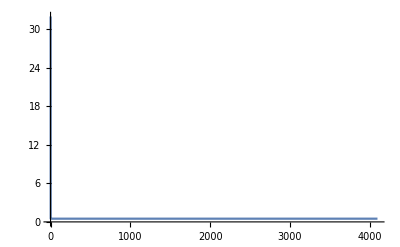

```mathematica
ListLinePlot@Abs[Fourier[v3]]
```

```mathematica
Sin
```

Sin::argx: Sin called with 2 arguments; 1 argument is expected.

General::stop: Further output of Sin::argx will be suppressed during this calculation.

```mathematica
a = Table[Sin[x],{x,0,1,0.1}]
```

{0.,0.0998334,0.198669,0.29552,0.389418,0.479426,0.564642,0.644218,0.717356,0.783327,0.841471}

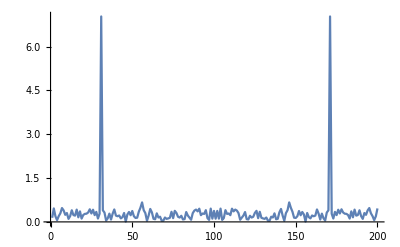

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->All]
```

```mathematica
(*AD采集进来，12bit数据，对其进行环路滤波*)
```

```mathematica
LowpassFilter[]
```

```mathematica
data = Table[SquareWave[i/100],{i,225}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

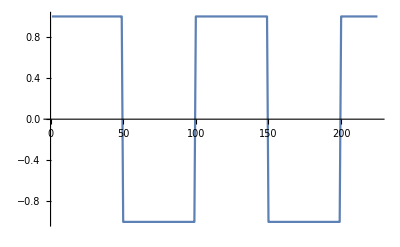

{2,2,0,1,1,0,1,0}

```mathematica
ListLinePlot[data]
```

```mathematica
v2a=Flatten[Table[v1[[i]],{i,15,24},50] ];(*100kx2*)
Length[v2a]
```

500

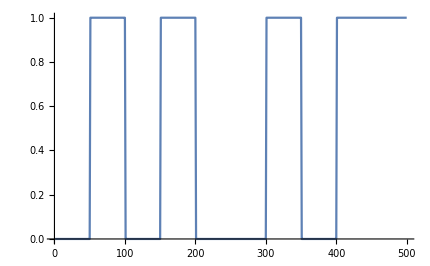

```mathematica
ListLinePlot[v2a]
```

```mathematica
noise = v3[[1;;500]];
```

```mathematica
ListLinePlot[noise];
```

```mathematica
adcdata = v2a + 1noise;
```

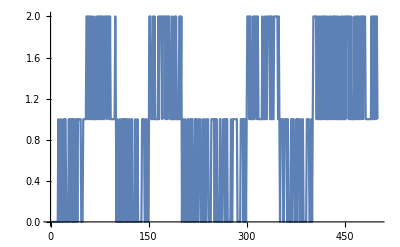

```mathematica
ListLinePlot[adcdata]
```

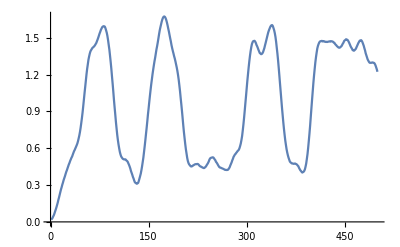

```mathematica
ListLinePlot[fitdata = LowpassFilter[adcdata,.1]]
```

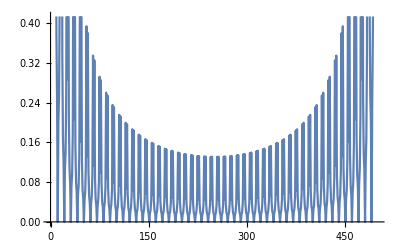

```mathematica
ListLinePlot[Abs[Fourier[v2a]]]
```

```mathematica
(*判断adc输入的幅值，取中值为判决电平*)
```

```mathematica
amp = Median[fitdata]
```

0.9936

```mathematica
Binar
```

```mathematica
bindata = Round[fitdata-(amp-0.5)]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

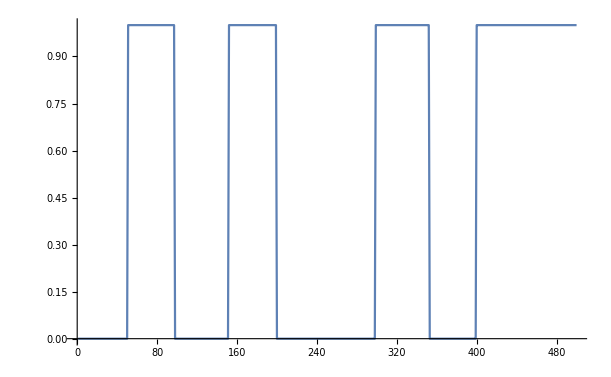

```mathematica
ListLinePlot[bindata]
```

```mathematica
freq = {10,20,30,40,50,60,70,80,90,100}*10^3
```

```mathematica
{10000,20000,30000,40000,50000,60000,70000,80000,90000,100000};
```